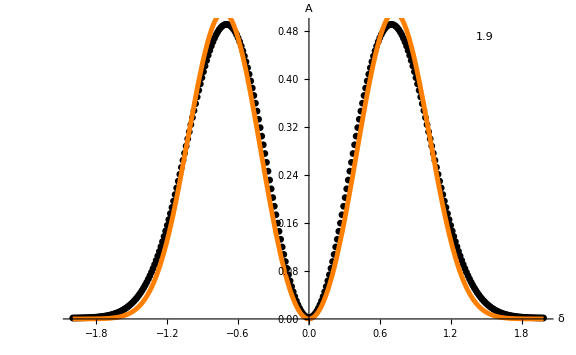

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/isotropism/isotropism.png

```mathematica
(*Isotropic dimensionless dissipation for X-wave; δ == χ^(1/3)Sin[θ] == (Subscript[k, 0] L)^(1/3)*Sin[θ]*)
δDissipation=ToExpression[GetData[config["isotropism","data"]]];
δbegining=First[δDissipation]⟦1⟧; δend=Last[δDissipation]⟦1⟧;
fittingFunction=Function[δ,a*δ^2 *Exp[-b*Abs[δ]^3 ]];
fit=FindFit[δDissipation,fittingFunction[δ],{a,b},δ];

experiment=ListPlot[δDissipation,
PlotRange->Full,
AxesLabel->{Style["δ",FontSize->40,Black],Style["A",FontSize->40,Black]},
LabelStyle->{FontSize->20},
PlotStyle->Black, 
PlotMarkers->{Automatic,7}];

theory=Plot[fittingFunction[δ]/.fit,{δ,δbegining,δend},
PlotRange->Full,
PlotStyle->{Orange,Thickness[0.006]},
PlotLegends->Placed[Text[Style[ToString[NumberForm[fittingFunction[δ]/.fit,3],TraditionalForm],Italic,25]],{0.86,0.94}]];

result=Show[{experiment,theory},ImageSize->Large]

SaveData[config["isotropism","directory"]<>"isotropism.png",result,"PNG"]
Clear[δDissipation,δbegining,δend,experiment,theory,fittingFunction,fit,result];
```

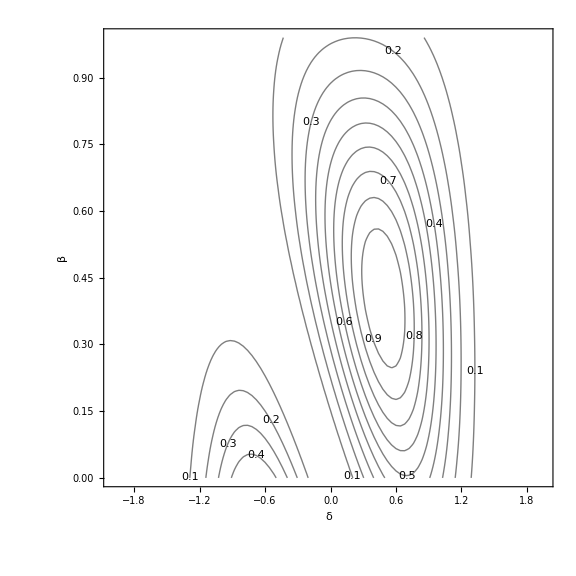

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/teta/teta.png

```mathematica
(*Anisotropic dimensionless dissipation for X-wave, η == 0; δ == χ^(1/3)Sin[θ] == (Subscript[k, 0] L)^(1/3)*Sin[θ], β == χ^(2/3)√u*)
δβDissipation=ToExpression[GetData[config["teta","data"]]];
result = ListContourPlot[δβDissipation,PlotRange->Full,ContourShading->None,ContourLabels->All,FrameLabel->{"δ","β"},RotateLabel->False,LabelStyle->(FontSize->17),ImageSize->Large]
SaveData[config["teta","directory"]<>"teta.png",result,"PNG"]
Clear[δβDissipation,result];
```

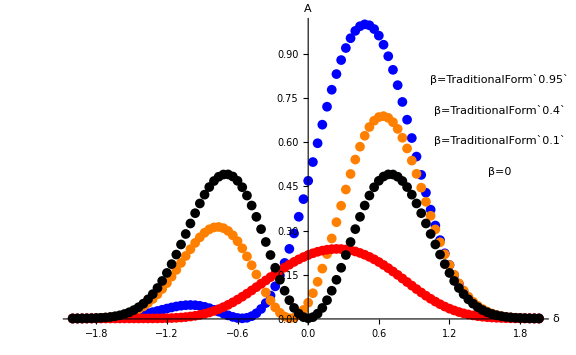

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/teta/sample2.png

```mathematica
(*Anisotropic dimensionless dissipation for X-wave, η == 0; δ == χ^(1/3)Sin[θ] == (Subscript[k, 0] L)^(1/3)*Sin[θ], β == χ^(2/3)√u*)
δβDissipation=ToExpression[GetData[config["teta","data"]]];
βbegining=First[δβDissipation]⟦2⟧;δnstep=Count[δβDissipation⟦All,2⟧,βbegining];

isotropism=ListPlot[δβDissipation⟦1;;δnstep,{1,3}⟧,
PlotRange->Full,ImageSize->Large,
AxesLabel->{Style["δ",FontSize->45,Black],Style["A",FontSize->45,Black]},
LabelStyle->{FontSize->25},
PlotStyle->Black,
PlotLegends->Placed[Text[Style["β=0",Black,Italic,FontSize->25]],{0.9,0.5}],
PlotMarkers->{Automatic,10}];

low=11;
lowField=ListPlot[δβDissipation⟦δnstep low+1;;δnstep(low+1),{1,3}⟧,
PlotRange->Full,ImageSize->Large,
AxesLabel->{Style["δ",FontSize->25,Black],Style["A",FontSize->25,Black]},
LabelStyle->{FontSize->20},
PlotStyle->Orange,
PlotLegends->Placed[Text[Style["β="<>ToString[δβDissipation⟦δnstep low,2⟧//N,TraditionalForm],Orange,Italic,FontSize->25]],{0.9,0.6}],
PlotMarkers->{Automatic,10}];

opt=41;
optimum=ListPlot[δβDissipation⟦δnstep opt+1;;δnstep(opt+1),{1,3}⟧,
PlotRange->Full,ImageSize->Large,
AxesLabel->{Style["δ",FontSize->25,Black],Style["A",FontSize->25,Black]},
LabelStyle->{FontSize->20},
PlotStyle->Blue,
PlotLegends->Placed[Text[Style["β="<>ToString[δβDissipation⟦δnstep opt,2⟧//N,TraditionalForm],Italic,Blue,FontSize->25]],{0.9,0.7}],
PlotMarkers->{Automatic,10}];

high=96;
highField=ListPlot[δβDissipation⟦δnstep high+1;;δnstep(high+1),{1,3}⟧,
PlotRange->Full,ImageSize->Large,
AxesLabel->{Style["δ",FontSize->45,Black],Style["A",FontSize->45,Black]},
LabelStyle->{FontSize->25},
PlotStyle->Red,
PlotLegends->Placed[Text[Style["β="<>ToString[δβDissipation⟦δnstep high,2⟧//N,TraditionalForm],Red,Italic,FontSize->25]],{0.9,0.8}],
PlotMarkers->{Automatic,10}];

(*ginzburg=Plot[Evaluate@Table[ⅇ^-α(1-ⅇ^-α)/.α->π β √(1/2 δ^2+√(β+1/4 δ^4)),{β,{0.1,0.4,0.95}}],{δ,-2,2},PlotRange->Full,PlotStyle->{Orange,Blue,Red}];*)

result=Show[optimum,lowField,highField,isotropism,(*ginzburg,*)ImageSize->Large]
SaveData[config["teta","directory"]<>"sample2.png",result,"PNG"]
Clear[δβDissipation,isotropism,low,lowField,opt,optimum,high,highField,result,βbegining,δnstep,ginzburg];
```

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/teta/zeroDissipation.png

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/teta/maxDissipation.png

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/teta/maxDissipationValue.png

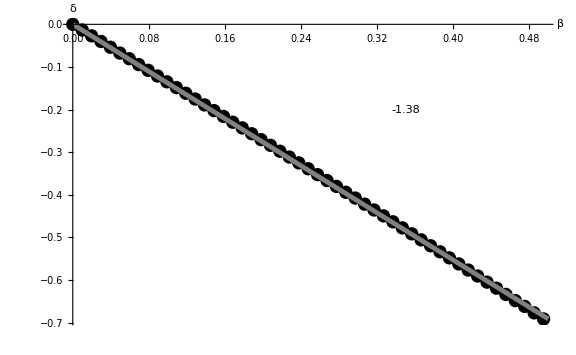
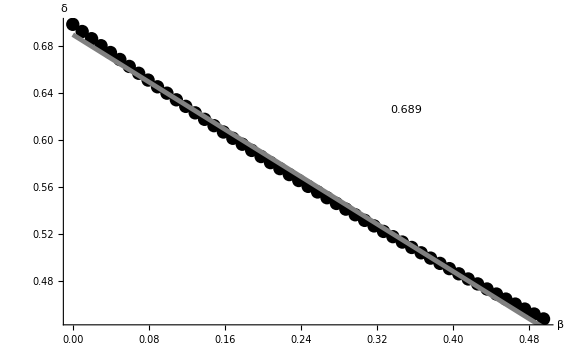
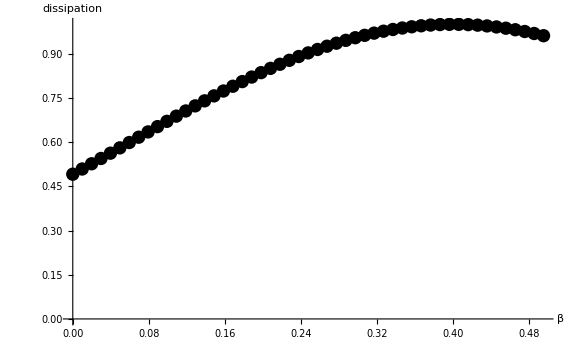

```mathematica
(*Anisotropic dimensionless dissipation for X-wave, η == 0; δ == χ^(1/3)Sin[θ] == (Subscript[k, 0] L)^(1/3)*Sin[θ], β == χ^(2/3)√u*)
δβDissipation=ToExpression[GetData[config["teta","data"]]];
δbegining=First[δβDissipation]⟦1⟧;δend=Last[δβDissipation]⟦1⟧;
βbegining=First[δβDissipation]⟦2⟧;βend=Last[δβDissipation]⟦2⟧;
δnstep=Count[δβDissipation⟦All,2⟧,βbegining];
βnstep=Length[δβDissipation]/δnstep;

βδMinimum={};
βδMaximum={};
βMaxDissipation={};

βmax=0.5;n=0;
ProgressIndicator[Dynamic[(β-βbegining)/(βmax-βbegining)]]
For[β=βbegining,β<βmax,β+=(βend-βbegining)/βnstep,
δDissipation=Table[{δβDissipation⟦n*βnstep+i,1⟧,δβDissipation⟦n*βnstep+i,3⟧},{i,1,δnstep}];
interpolation=Interpolation[δDissipation];
δmin=x/.Last[FindMinimum[{interpolation[x],δbegining<x<δend},{x,-0.1}]];
βδMinimum=Append[βδMinimum,{β,δmin}];
δmax=x/.Last[FindMaximum[{interpolation[x],δbegining<x<δend},{x,0.4}]];
βδMaximum=Append[βδMaximum,{β,δmax}];
maxDissipation=First[FindMaximum[{interpolation[x],δbegining<x<δend},{x,0.4}]];
βMaxDissipation = Append[βMaxDissipation,{β,maxDissipation}];
n+=1;
];
Clear[β,δ,n,βnstep,δnstep,δDissipation,δbegining,βend,δend,δmin,δmax]

experiment=ListPlot[βδMinimum,PlotRange->Full,AxesLabel->{"β","δ"},LabelStyle->{FontSize->14},PlotStyle->Black];
fittingFunction=Function[β,a*β];
fit=FindFit[βδMinimum,fittingFunction[β],a,β];

theory=Plot[fittingFunction[β]/.fit,{β,βbegining,βmax},PlotRange->Full,PlotStyle->{Gray,Thickness[0.006]},
PlotLegends->Placed[Text[Style[ToString[NumberForm[fittingFunction[β]/.fit,3],TraditionalForm],Italic,20]],{0.7,0.7}]];

βδMinimumResult=Show[{experiment,theory},ImageSize->Large];
SaveData[config["teta","directory"]<>"zeroDissipation.png",βδMinimumResult,"PNG"]

experiment=ListPlot[βδMaximum,PlotRange->Full,AxesLabel->{"β","δ"},LabelStyle->{FontSize->14},PlotStyle->Black];
fittingFunction=Function[β,a+b*β];
fit=FindFit[βδMaximum,fittingFunction[β],{a,b},β];
theory=Plot[fittingFunction[β]/.fit,{β,βbegining,βmax},PlotRange->Full,PlotStyle->{Gray,Thickness[0.006]},
PlotLegends->Placed[Text[Style[ToString[NumberForm[fittingFunction[β]/.fit,3],TraditionalForm],Italic,20]],{0.7,0.7}]];

βδMaximumResult=Show[{experiment,theory},ImageSize->Large];
SaveData[config["teta","directory"]<>"maxDissipation.png",βδMaximumResult,"PNG"]

experiment=ListPlot[βMaxDissipation,PlotRange->Full,AxesLabel->{"β","dissipation"},LabelStyle->{FontSize->14},PlotStyle->Black];

βMaxDissipationResult=Show[{experiment},ImageSize->Large];
SaveData[config["teta","directory"]<>"maxDissipationValue.png",βMaxDissipationResult,"PNG"]

{βδMinimumResult,βδMaximumResult,βMaxDissipationResult}
Clear[δβDissipation,βδMinimum,βδMaximum,βMaxDissipation,βbegining,βmax,experiment,theory,fittingFunction,fit,βδMinimumResult,βδMaximumResult,βMaxDissipationResult];
```

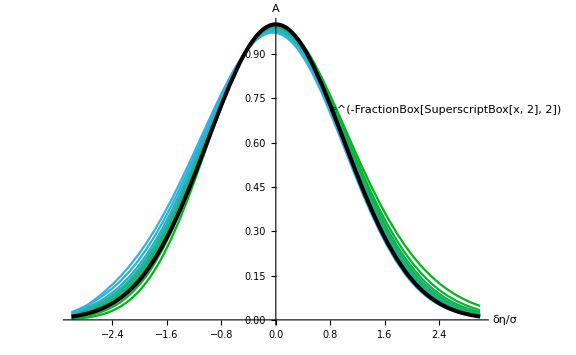

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/eta/high-field.png

```mathematica
(*Anisotropic dimensionless dissipation for O-wave, θ == 0; σ == (2 √2 Subscript[πχ, 0] u^(1/4))^(-1/2)*)
ηχDissipation=ToExpression[GetData[config["eta","high-field"]]];
χbegining=First[ηχDissipation]⟦2⟧;
ηnstep=Count[ηχDissipation⟦All,2⟧,χbegining];
χnstep=Length[ηχDissipation]/ηnstep;

interpolation=Table[Interpolation[ηχDissipation⟦(i-1) ηnstep+1;;i ηnstep,{1,3}⟧],{i,1,χnstep}];
experiment=Plot[Evaluate@Table[interpolation⟦i⟧[x],{i,1,Length[interpolation]}],{x,-3,3},
PlotRange->Full,
AxesLabel->{Style["δη/σ",FontSize->25,Black],Style["A",FontSize->25,Black]},
LabelStyle->{FontSize->25},
PlotStyle->Table[RGBColor[0.2i,0.7,i],{i,0.1,1,0.9/Length[interpolation]}]];
theory=Plot[ⅇ^(-x^2/2),{x,-3,3},PlotStyle->{Black,Thickness[0.005]},PlotLegends->Placed[Text[Style["ⅇ^(-FractionBox[SuperscriptBox[x, 2], 2])",Italic,FontSize->45]],{0.9,0.7}]];
result=Show[{experiment,theory},ImageSize->Large]
SaveData[config["eta","directory"]<>"high-field.png",result,"PNG"]
Clear[ηχDissipation,χbegining,ηnstep,χnstep,interpolation,experiment,theory,result];
```

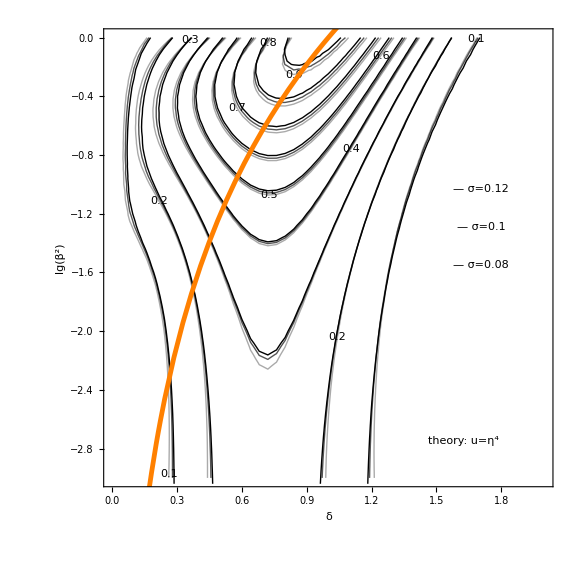

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/eta/low-field.png

```mathematica
(*σηυDissipation=ToExpression[GetData[config["eta","low-field"]]];*)
experiment=Show[Table[
Legended[ListContourPlot[σηυDissipation⟦i,2⟧,PlotRange->Full,FrameLabel->{Style["δ",FontSize->30,Black],Style["lg(β^2)",FontSize->30,Black]},
ContourShading->None,ContourLabels->If[i==1,All,None],ContourStyle->RGBColor[0,0,0,i Length[σηυDissipation]^-1],
(*RotateLabel->False,*)LabelStyle->(FontSize->17),ImageSize->Large],
Placed[Text[Style["— σ="<>ToString[σηυDissipation⟦i,1⟧],Italic,25,RGBColor[0,0,0,i Length[σηυDissipation]^-1]]],{0.84,0.4+i Length[σηυDissipation]^-1/4}]],
{i,1,Length[σηυDissipation]}]];
theory=Legended[Plot[Log[10,η^4],{η,0,2},
PlotRange->Full,
PlotStyle->{Orange,Thickness[0.006]}],
Placed[Text[Style[TraditionalForm["theory: u=η^4"],Italic,25,Orange]],{0.8,0.1}]];

result=Show[experiment,theory,ImageSize->Large]
SaveData[config["eta","directory"]<>"low-field.png",result,"PNG"]
Clear[(*σηυDissipation,*)experiment,theory,result];
```

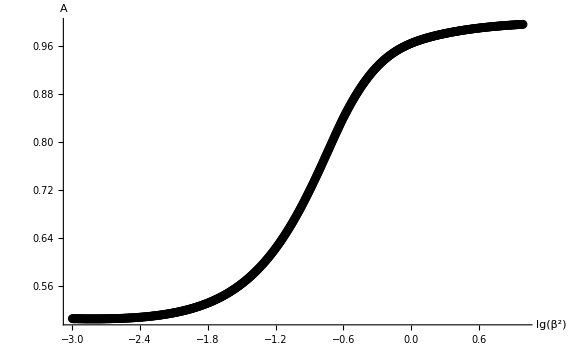
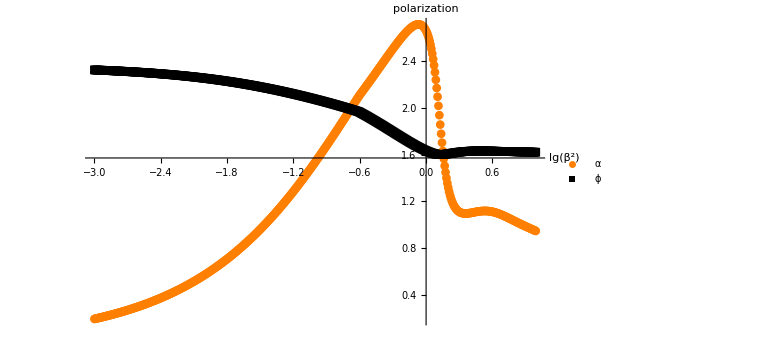

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/eta/low-field-dissipation.png

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/eta/low-field-polarization.png

```mathematica
polarization=ToExpression[GetData[config["eta","polarization"]]];

d=ListPlot[polarization⟦2⟧,PlotRange->Full,ImageSize->Large,
AxesLabel->{Style["lg(β^2)",FontSize->40,Black],Style["A",FontSize->40,Black]},
LabelStyle->(FontSize->25),
PlotStyle->Black];

p=ListPlot[{polarization⟦1,All,{1,2}⟧,polarization⟦1,All,{1,3}⟧},PlotRange->Full,ImageSize->Large,
PlotLegends->Placed[{"α","ϕ"},{0.9,0.75}],
AxesOrigin->{0,π/2},
AxesLabel->{Style["lg(β^2)",FontSize->40,Black],Style["polarization",FontSize->40,Black]},
LabelStyle->(FontSize->25),
PlotMarkers->Automatic,
PlotStyle->{Orange,Black}];
{d,p}
SaveData[config["eta","directory"]<>"low-field-dissipation.png",d,"PNG"]
SaveData[config["eta","directory"]<>"low-field-polarization.png",p,"PNG"]
Clear[polarization,d,p];
```